# Singularities in complex analysis:

## Simple poles, branch points, essential singularities, and clusters points of singularities

I recommend clicking on the axes to rotate the pictures around so you can see the structure of the surfaces defined by this function. Riemann was able to see all this in his head; ordinary mortals like you and I need computer graphics.

## A simple pole

#### f(z)=(z-1)^-1

There is a singularity at z=1

```mathematica
Plot3D[Re[1/(x+I y-1)],{x,-2,2},{y,-2,2},PlotRange->{-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Im[1/(x+I y-1)],{x,-2,2},{y,-2,2},PlotRange->{-3,3}]
```

-Graphics3D-

#### Another simple pole: f(z)=(z-1)^-4

There is a singularity at z=1

```mathematica
Plot3D[Re[1/(x+I y-1)^4],{x,-2,2},{y,-2,2},PlotRange->{-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Im[1/(x+I y-1)^4],{x,-2,2},{y,-2,2},PlotRange->{-3,3}]
```

-Graphics3D-

## A branch point: the complex logarithm

Recall that log(z)=log(r)+i θ.

#### The real part is simple enough.

As r→ 0, the real part of the logarithm goes to negative infinity

```mathematica
RevolutionPlot3D[Re[Log[r]+I θ],{r,0,1},{θ,-2π,2π}]
```

-Graphics3D-

#### The imaginary part is a multi-valued function of z

The is because the polar angle θ isn’t uniquely defined for a given z, since z=r e^(i θ+ 2 π n i) for any integer n. We can always replace θ by θ+2 π n i and get the same z, so we’re allowed to take θ to be any real number, not just numbers in an interval of length 2 π. 

The result is a plot that looks like a “spiral staircase.” Here’s the plot on the interval [-2π, 2π].

```mathematica
RevolutionPlot3D[Im[Log[r]+I θ],{r,0,1},{θ,-2π,2π}]
```

-Graphics3D-

To get a single-valued function, we have to restrict θ to one turn around the spiral staircase. This is called choosing a “branch” of the function. For the logarithm, the conventional choice is to cut the staircase along the negative real axis; the variable θ is restricted to the interval [-π,π]. There will be a discontinuity at the “cut”. 

Because of the discontinuity at a branch cut, we can’t do integrals on curves that cross a branch cut.

```mathematica
RevolutionPlot3D[Im[Log[r Exp[I θ]]],{r,0,1},{θ,-π,π},PlotPoints->60]
```

-Graphics3D-

Notice that the imaginary part is undefined at z=0. 

Because we need to make a branch cut anchored at z=0, we call this point a “branch point” singularity

## Another branch point: the complex square root

You already know the square root is multi-valued even as a function of a positive real variable: √4=±2, and so on. Viewing the square root in the complex plane helps us understand how that happens.

Here is the real part. The surface intersects itself along the negative real axis. The black curve shows the positive and negative square roots along the positive real axis: both are on this single surface.

```mathematica
Show[RevolutionPlot3D[Re[Sqrt[r]Exp[I θ/2]],{r,0,1},{θ,-2π,2π},PlotPoints->60],ParametricPlot3D[{t^2,0,t},{t,-1,1},PlotStyle->{Thick,Black}]]
```

-Graphics3D-

Now the imaginary part. Can you understand what’s going on? What’s happening along the real axis, and why?

```mathematica
RevolutionPlot3D[Im[Sqrt[r]Exp[I θ/2]],{r,0,1},{θ,-2π,2π},PlotPoints->60]
```

-Graphics3D-

#### We can put a branch cut along the negative real axis

To get a single-valued function, we impose a branch cut. The conventional choice is along the negative real axis. Zero is the branch point (regardless of which branch cut we choose). The real part of √z is continuous but not differentiable across the branch cut.

The black curve shows ±√x along the x axis. You can see how the chosen branch of the complex function selects the positive square root: only the positive square root still lies on the surface.

```mathematica
Show[RevolutionPlot3D[Re[Sqrt[r]Exp[I θ/2]],{r,0,1},{θ,-π,π},PlotPoints->60,PlotRange->{-1,1}],ParametricPlot3D[{t^2,0,t},{t,-1,1},PlotStyle->{Thick,Black}]]
```

-Graphics3D-

The imaginary part is not continuous across the branch cut

```mathematica
RevolutionPlot3D[Im[Sqrt[r Exp[I θ]]],{r,0,1},{θ,-π,π}]
```

-Graphics3D-

## An essential singularity: the marvelous e^(-1/z)

```mathematica
Z[r_,θ_]=r Exp[I θ]
```

ⅇ^(ⅈ θ) r

```mathematica
RevolutionPlot3D[Re[Exp[-1/ Z[r,θ]]],{r,0.1,1},{θ,0,2π},PlotPoints->200]
```

-Graphics3D-

#### Along the positive real axis

General::munfl: exp(-48951.) is too small to represent as a normalized machine number; precision may be lost.

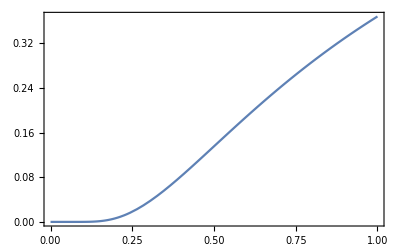

```mathematica
Plot[Exp[-1/x],{x,0,1}]
```

#### Along the negative real axis

Note the scale

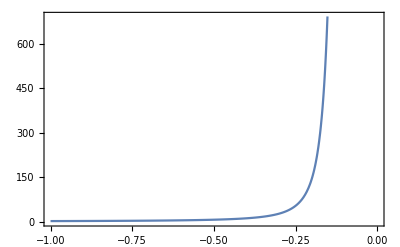

```mathematica
Plot[Exp[-1/x],{x,-1,0},PlotPoints->200]
```

#### Along the imaginary axis (real part of f)

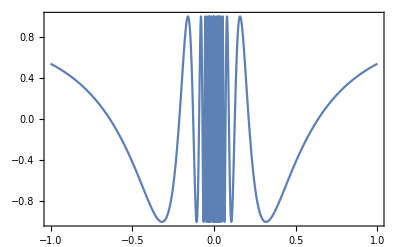

```mathematica
Plot[Cos[1/y],{y,-1,1},PlotPoints->200]
```

#### Along the ray rotated 85 degrees from the positive real axis

Here we see wild oscillations with decreasing amplitude as z→ 0

```mathematica
α=85π/180
```

(17 π)/36

General::munfl: exp(-4266.37+48764.8 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

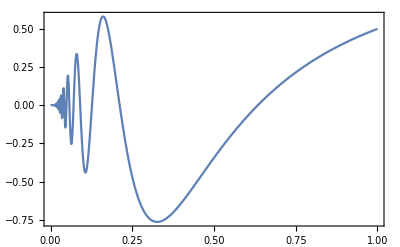

```mathematica
Plot[Re[Exp[-1/Z[r,α]]],{r,0,1}]
```

#### Along the ray rotated 91 degrees from the positive real axis

Here we see wild oscillations with increasing amplitude as z→ 0

```mathematica
α=91π/180
```

(91 π)/180

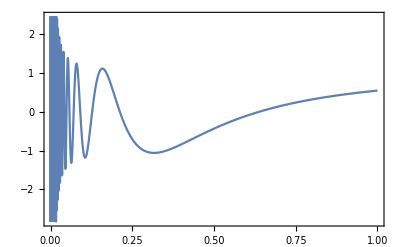

```mathematica
Plot[Re[Exp[-1/Z[r,α]]],{r,0,1},PlotPoints->200]
```

## A cluster of singularities

In this function, we have many singularities whose locations cluster around z=0

f(z)=∑_(n=0)^∞ (z-1/n)^-2.

```mathematica
f[M_,z_]:=Sum[1/(z-1/n^2)^2,{n,1,M}]
```

Here’s a partial sum with only 10 singularities

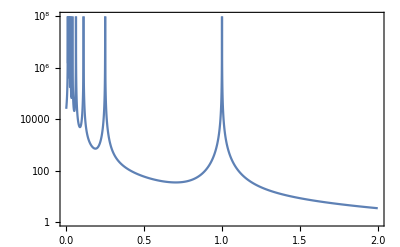

```mathematica
LogPlot[f[10,x],{x,0,2},PlotRange->{1,10^8},PlotPoints->1000]
```

20 singularities

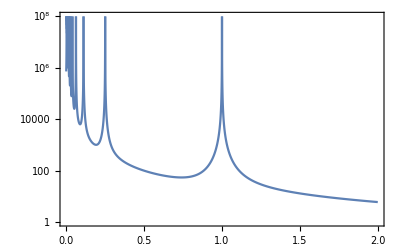

```mathematica
LogPlot[f[20,x],{x,0,2},PlotRange->{1,10^8},PlotPoints->1000]
```

In the limit, it’s impossible to place an open interval around zero that does not contain a singularity.